## naloga1

```mathematica
izraz=(x^5-2x^2+3x+4)/(x^5-2x-1)
izraz/.x-> 2
izraz/.x-> {1,2,3,4}
izraz/.{x-> 1,x-> 2,x-> 3,x-> 4}
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

34/27

{-3,34/27,119/118,144/145}

-3

```mathematica
f[x_]:=(x^5-2x^2+3x+4)/(x^5-2x-1)
Table[3*i,{i,1,5}]
```

{3,6,9,12,15}

## naloga 2

```mathematica
sez=Table[10*i,{i,1,7}]
```

{10,20,30,40,50,60,70}

```mathematica
sez
```

{10,20,30,40,50,60,70}

```mathematica
sez[[3]]
```

30

```mathematica
Take[sez,{2,3}]
```

{20,30}

```mathematica
Drop[sez,{2,3}]
```

{10,40,50,60,70}

```mathematica
Part[sez,{1,3,5}]
```

{10,30,50}

```mathematica
Part[sez,3]
```

30

```mathematica
sez[[{1,3,5}]]
```

{10,30,50}

```mathematica
Take[sez,{1,3}]
```

{10,20,30}

```mathematica
Take[sez,{-2,-1}]
```

{60,70}

```mathematica
Take[sez,{2,4}]
```

{20,30,40}

```mathematica
Drop[sez,{2,3,5}]
```

{10,30,40,50,60,70}

## naloga 3

```mathematica
ClearAll[x,a,sez]
```

```mathematica
sez={x^6,x^2,a}
```

{x^6,x^2,a}

```mathematica
sez/.{x-> 3}
```

{729,9,a}

```mathematica
sez/.{x-> x^2}
```

{x^12,x^4,a}

```mathematica
sez/.{x^2-> x}
```

{x^6,x,a}

```mathematica
sez/.x-> {1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez/.{x->3,a-> x}
```

{729,9,x}

```mathematica
sez//.{x->3,a-> x}
```

{729,9,3}

```mathematica
ReplaceRepeated[sez,{x->3,a-> x}]
```

{729,9,3}

```mathematica
{sez/.x->1,sez/.x->2,sez/.x->3,}
```

{{1,1,a},{64,4,a},{729,9,a},Null}

```mathematica
Table[sez/.x->i,{i,1,10}]
```

{{1,1,a},{64,4,a},{729,9,a},{4096,16,a},{15625,25,a},{46656,36,a},{117649,49,a},{262144,64,a},{531441,81,a},{1000000,100,a}}

## 4. naloga

```mathematica
odvod1=D[x^5+4x^3-9,x]
```

12 x^2+5 x^4

```mathematica
odvod1/.x->1
```

17

```mathematica
odvod1/.x->5
```

3425

```mathematica
D[E^(x^(1/4))]/. {{x->1}, {x->2}}
```

{ⅇ,ⅇ^(2^(1/4))}

```mathematica
Abs[x+1]
```

Abs[1+x]

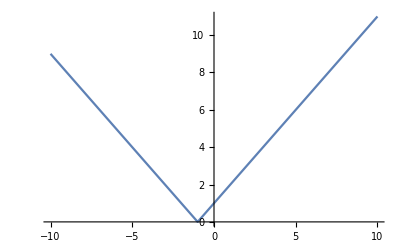

```mathematica
Plot[Abs[x+1], {x, -10, 10} ]
```

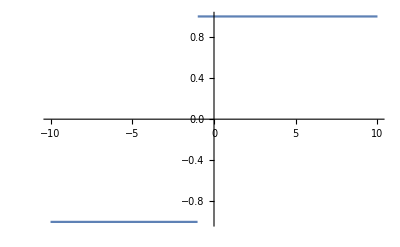

```mathematica
Plot[Sign[x+1], {x, -10, 10} ]
```

```mathematica
FullSimplify[D[Abs[x+1], x], Element[x, Reals]]
```

Sign[1+x]

```mathematica
ClearAll
```

ClearAll

```mathematica
D[ax^2+3b]
```

ax^2+3 b

```mathematica
D[ax^2+3b,x]/. {{x->1},{x->2}}
```

{0,0}

## Naloga 5

```mathematica
f[x_]:=x^3Log[4x+5]
```

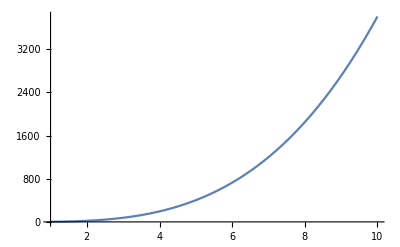

```mathematica
Plot[f[x], {x, 1, 10}]
```

```mathematica
x0 = 5
```

```mathematica
f[x0]
```

125 Log[25]

```mathematica
k0=D[f[x], x]/.x->x0
```

20+75 Log[25]

```mathematica
y==k0 x+n/.{x->x0,y->f[x0]}
```

125 Log[25]==n+5 (20+75 Log[25])

```mathematica
f[x0]==k0 x0+n
```

125 Log[25]==n+5 (20+75 Log[25])

```mathematica
enacba = f[x0]==k0 x0+n
```

125 Log[25]==n+5 (20+75 Log[25])

```mathematica
resitev=Solve[enacba,n]
```

{{n→-50 (2+5 Log[25])}}

```mathematica
n0=n/.resitev//First
```

-50 (2+5 Log[25])

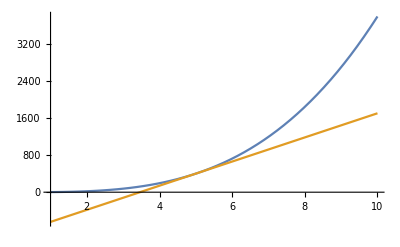

```mathematica
Plot[{f[x],k0 x+n0},{x,1,10}]
```

```mathematica
narisi[f_,x0_,x_,zac_,kon_]:=Module[{k0,n,enacba,resitev,n0},
k0=D[f[x], x]/.x->x0;
enacba = f[x0]==k0 x0+n;
resitev=Solve[enacba,n];
n0=n/.resitev//First;
Plot[{f[x],k0 x+n0},{x,zac,kon}]
]
```

```mathematica
narisi[f,x0,x,0,10]
```

20+75 Log[25]

```mathematica
narisi[f,x0,x,0,10]
```

{{n$39616→-50 (2+5 Log[25])}}

```mathematica
narisi[f,x0,x,0,10]
```

-50 (2+5 Log[25])

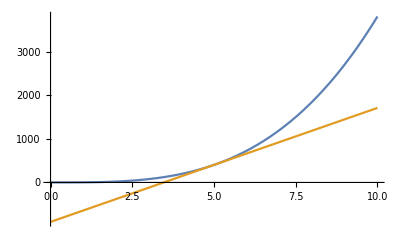

```mathematica
narisi[f,x0,x,0,10]
```

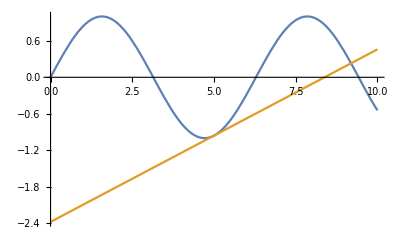

```mathematica
narisi[Sin,5,x,0,10]
```

## Naloga 6

```mathematica
izraz=(x^3-4x^2+2x+4)/(x^5-9x-14)
```

(4+2 x-4 x^2+x^3)/(-14-9 x+x^5)

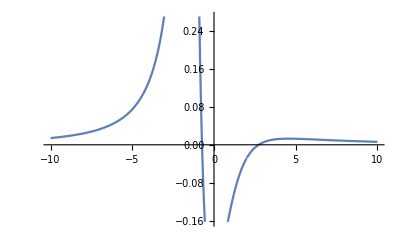

```mathematica
Plot[izraz,{x,-10,10}]
```

```mathematica
Solve[x^5-9x-14==0,x]//N
```

{{x→2.},{x→-1.29339-0.551316 ⅈ},{x→-1.29339+0.551316 ⅈ},{x→0.29339-1.85876 ⅈ},{x→0.29339+1.85876 ⅈ}}

```mathematica
FullSimplify[izraz]
```

(-2+(-2+x) x)/(7+x (2+x) (4+x^2))

```mathematica
x^3-4x^2+2x+4/.x->2
```

0

```mathematica
x^5-9x-14/.x->2
```

0

```mathematica
izraz/.x->1.99
```

-0.0287719

```mathematica
Limit[izraz,x-> 2]//N
```

-0.028169

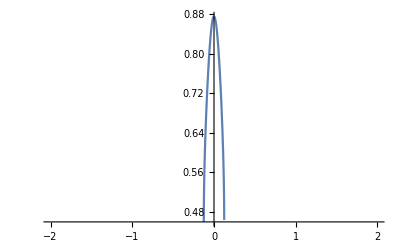

```mathematica
Plot[ArcTan[7x]/ArcSin[8x],{x,-2,2}]
```

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x-> 0]
```

7/8

```mathematica
Limit[(x^2-25)Cot[Pi x],x-> 5]
```

10/π

```mathematica
Limit[(1+Cos [x])/(2Sqrt[Pi x]-Pi-x),x-> Pi]//N
```

-6.28319

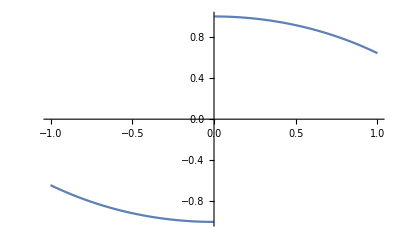

```mathematica
Plot[Abs[x]Cot[x],{x,-1,1}]
```

```mathematica
Limit[Abs[x]Cot[x],x-> 0,Direction->"FromAbove"]
```

1

```mathematica
Limit[Abs[x]Cot[x],x-> 0,Direction->"FromBelow"]
```

-1

## Naloga 7

```mathematica
f[x_]:=(x^2-1)/(x^2-4)
```

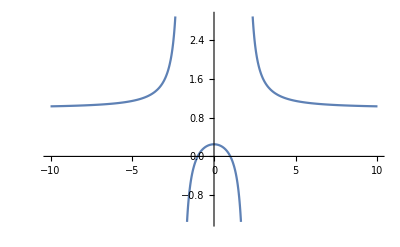

```mathematica
Plot[(x^2-1)/(x^2-4),{x,-10,10}]
```

#### Ničle :

Izračunamo f (x) = 0

```mathematica
Solve[f[x]==0,x]
```

{{x→-1},{x→1}}

Funkcija ima ničli v - 1 in 1.

#### Poli:

Pole izračunamo kot ničle imenovalca.

```mathematica
Solve[1/f[x]==0,x]
```

{{x→-2},{x→2}}

```mathematica
Limit[f[x],x->2,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[f[x],x->2,Direction->"FromAbove"]
```

∞

```mathematica
Limit[f[x],x->2,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[f[x],x->2,Direction->"FromAbove"]
```

∞

Pola sta v točkah - 2 in 2. Ko se bližamo iz negativne neskončnosti proti polu - 2, gre

## Naloga 8.

```mathematica
Solve[{x^4+x^3-x==0,x>0},x]//N
```

{{x→0.754878}}

```mathematica
Solve[x^4+x^3-x==0&&x>0,x]
```

{{x→Root0.755Root[-1+#1^2+#1^3&,1]0.7548776662466927}}

```mathematica
Reduce[x^4+x^3-x==0&&x>0,x]
```

x==Root0.755Root[-1+#1^2+#1^3&,1]0.7548776662466927

## Naloga 9.

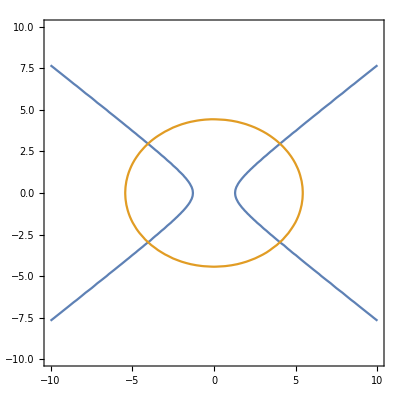

```mathematica
ContourPlot[{3x^2-5y^2==5,2x^2+3y^2==59},{x,-10,10},{y,-10,10}]
```

```mathematica
x0=
x/.Solve[{3x^2-5y^2==5,2x^2+3y^2==59,x>0,y>0},{x,y}]//First
```

√(310/19)

```mathematica
f1=y/.Solve[{3x^2-5y^2==5,x>0,y>0},y]//First
```

ConditionalExpression[(√(-5+3 x^2))/(√5),x>√(5/3)]

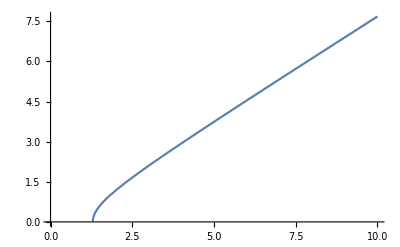

```mathematica
Plot[f1,{x,0,10}]
```

```mathematica
f2=y/.Solve[{2x^2+3y^2==59,x>0,y>0},y]//First
```

ConditionalExpression[(√(59-2 x^2))/(√3),0<x<√(59/2)]

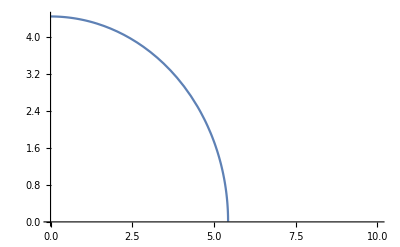

```mathematica
Plot[f2,{x,0,10}]
```

```mathematica
k1=D[f1,x]/.x->x0
k2=D[f2,x]/.x->x0
```

3 √(62/835)

-(2 √(310/167))/3

```mathematica
kot=Abs[ArcTan[k1]-ArcTan[k2]]//N
```

1.42269

```mathematica
kot/Degree
```

81.5141